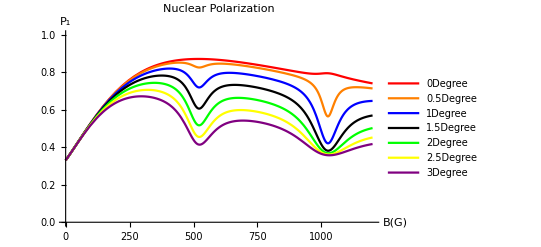

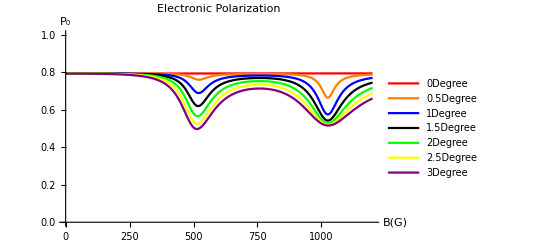

```mathematica
Q=-4.945;Cp=-40;Cv=-23;De=1420;gammae=2.802;gamman=-0.003;(*Subscript[T, 1]=1;Subscript[T, 20]=33;Subscript[T, 21]=1;*)
Dg=2870;Γ=66;Subscript[Γ, 5]=Γ;Subscript[Γ, 0]=7.9;Subscript[Γ, 1]=53;Subscript[Γ, 3]=1.0;Subscript[Γ, 4]=0.7;Ap=-2.162;Av=-2.62;theta=π*20/180;(*psi=π*3/180;*)
He={{Cp+De+Bz gamman+Q+Bz gammae Cos[psi],0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,0,0,0},{0,De+Bz gammae Cos[psi],0,Cv,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,0,0},{0,0,-Cp+De-Bz gamman+Q+Bz gammae Cos[psi],0,Cv,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,0},{gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Cv,0,Bz gamman+Q,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0},{0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Cv,0,0,0,Cv,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0},{0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,-Bz gamman+Q,0,Cv,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2))},{0,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Cv,0,-Cp+De+Bz gamman+Q-Bz gammae Cos[psi],0,0},{0,0,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Cv,0,De-Bz gammae Cos[psi],0},{0,0,0,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,Cp+De-Bz gamman+Q-Bz gammae Cos[psi]}};
Hg={{Ap+Dg+Bz gamman+Q+Bz gammae Cos[psi],0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,0,0,0},{0,Dg+Bz gammae Cos[psi],0,Av,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,0,0},{0,0,-Ap+Dg-Bz gamman+Q+Bz gammae Cos[psi],0,Av,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,0},{gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Av,0,Bz gamman+Q,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0},{0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Av,0,0,0,Av,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0},{0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,-Bz gamman+Q,0,Av,gammae ((Bz Cos[theta] Sin[psi])/(√2)-(ⅈ Bz Sin[psi] Sin[theta])/(√2))},{0,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Av,0,-Ap+Dg+Bz gamman+Q-Bz gammae Cos[psi],0,0},{0,0,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),Av,0,Dg-Bz gammae Cos[psi],0},{0,0,0,0,0,gammae ((Bz Cos[theta] Sin[psi])/(√2)+(ⅈ Bz Sin[psi] Sin[theta])/(√2)),0,0,Ap+Dg-Bz gamman+Q-Bz gammae Cos[psi]}};
H=ConstantArray[0,{21,21}];For[i=1,i≤9,i++,For[j=1,j≤9,j++,H[[i,j]]=Hg[[i,j]];]](*1-6ground states, 7-9 singlet, 10-15 excited states*)
For[i=13,i≤21,i++,For[j=13,j≤21,j++,H[[i,j]]=He[[i-12,j-12]];]]
(*H[[7,7]]=E1;*)Rho=Array[rho,{21,21}];
Sigma=Table[0,{100},{21},{21}];
For[i=1,i≤9,i++,Sigma[[i]][[i,i+12]]=1;]
For[i=10,i≤12,i++,Sigma[[i]][[i,i+3]]=1;]
For[i=13,i≤15,i++,Sigma[[i]][[i-3,i+3]]=1;]
For[i=16,i≤18,i++,Sigma[[i]][[i-6,i+3]]=1;]
For[i=19,i≤21,i++,Sigma[[i]][[i-18,i-9]]=1;]
For[i=22,i≤24,i++,Sigma[[i]][[i-18,i-12]]=1;]
For[i=25,i≤27,i++,Sigma[[i]][[i-18,i-15]]=1;]
For[i=28,i≤36,i++,Sigma[[i]][[i-15,i-27]]=1;]
For[i=37,i≤39,i++,Sigma[[i]][[i-33,i-24]]=1;]
For[i=40,i≤42,i++,Sigma[[i]][[i-33,i-27]]=1;]
For[i=43,i≤45,i++,Sigma[[i]][[i-42,i-27]]=1;]
For[i=46,i≤48,i++,Sigma[[i]][[i-39,i-30]]=1;]
For[i=49,i≤51,i++,Sigma[[i]][[i-48,i-30]]=1;]
For[i=52,i≤54,i++,Sigma[[i]][[i-48,i-33]]=1;]

(*1-9: spontaneous decay, spin-conversing, 10-18:excited states-singlet, 19-27: singlet-ground states*, 19-24: optical excitation; 25-*)
L=ConstantArray[0,{21,21}];
For[i=1,i≤9,i++,L=L+Γ/2*(2*Sigma[[i]].Rho.Transpose[Sigma[[i]]]-Transpose[Sigma[[i]]].Sigma[[i]].Rho-Rho.Transpose[Sigma[[i]]].Sigma[[i]])];
For[i=13,i≤15,i++,L=L+Subscript[Γ, 0]/2*(2*Sigma[[i]].Rho.Transpose[Sigma[[i]]]-Transpose[Sigma[[i]]].Sigma[[i]].Rho-Rho.Transpose[Sigma[[i]]].Sigma[[i]])];For[i=10,i≤12,i++,L=L+Subscript[Γ, 1]/2*(2*Sigma[[i]].Rho.Transpose[Sigma[[i]]]-Transpose[Sigma[[i]]].Sigma[[i]].Rho-Rho.Transpose[Sigma[[i]]].Sigma[[i]])];
For[i=16,i≤18,i++,L=L+Subscript[Γ, 1]/2*(2*Sigma[[i]].Rho.Transpose[Sigma[[i]]]-Transpose[Sigma[[i]]].Sigma[[i]].Rho-Rho.Transpose[Sigma[[i]]].Sigma[[i]])];
For[i=22,i≤24,i++,L=L+Subscript[Γ, 3]/2*(2*Sigma[[i]].Rho.Transpose[Sigma[[i]]]-Transpose[Sigma[[i]]].Sigma[[i]].Rho-Rho.Transpose[Sigma[[i]]].Sigma[[i]])];
For[i=19,i≤21,i++,L=L+Subscript[Γ, 4]/2*(2*Sigma[[i]].Rho.Transpose[Sigma[[i]]]-Transpose[Sigma[[i]]].Sigma[[i]].Rho-Rho.Transpose[Sigma[[i]]].Sigma[[i]])];
For[i=25,i≤27,i++,L=L+Subscript[Γ, 4]/2*(2*Sigma[[i]].Rho.Transpose[Sigma[[i]]]-Transpose[Sigma[[i]]].Sigma[[i]].Rho-Rho.Transpose[Sigma[[i]]].Sigma[[i]])];
For[i=28,i≤36,i++,L=L+Subscript[Γ, 5]/2*(2*Sigma[[i]].Rho.Transpose[Sigma[[i]]]-Transpose[Sigma[[i]]].Sigma[[i]].Rho-Rho.Transpose[Sigma[[i]]].Sigma[[i]])];
For[i=37,i≤54,i++,L=L+0.01*Γ/2*(2*Sigma[[i]].Rho.Transpose[Sigma[[i]]]-Transpose[Sigma[[i]]].Sigma[[i]].Rho-Rho.Transpose[Sigma[[i]]].Sigma[[i]])];
M=-ⅈ*(H.Rho-Rho.H)+L;M[[21,21]]=Rho[[1,1]]+Rho[[2,2]]+Rho[[3,3]]+Rho[[4,4]]+Rho[[5,5]]+Rho[[6,6]]+Rho[[7,7]]+Rho[[8,8]]+Rho[[9,9]]+Rho[[10,10]]+Rho[[11,11]]+Rho[[12,12]]+Rho[[13,13]]+Rho[[14,14]]+Rho[[15,15]]+Rho[[16,16]]+Rho[[17,17]]+Rho[[18,18]]+Rho[[19,19]]+Rho[[20,20]]+Rho[[21,21]]-1;
F[Bz_]:=Re[(Rho[[16,16]]/(Rho[[16,16]]+Rho[[17,17]]+Rho[[18,18]]))/.Solve[Flatten[M==ConstantArray[0,{21,21}]],Flatten[Rho]][[1]]];
F1[Bz_]:=Re[((Rho[[16,16]]+Rho[[17,17]]+Rho[[18,18]])/(Rho[[16,16]]+Rho[[17,17]]+Rho[[18,18]]+Rho[[19,19]]+Rho[[20,20]]+Rho[[21,21]]+Rho[[13,13]]+Rho[[14,14]]+Rho[[15,15]]))/.Solve[Flatten[M==ConstantArray[0,{21,21}]],Flatten[Rho]][[1]]];
psi=π*0/180;
Fig0=Plot[F[Bz],{Bz,0,1200},PlotStyle->Red,PlotRange->{0,1},PlotLegends->{"0Degree"}];
psi=π*0.5/180;
Fig01=Plot[F[Bz],{Bz,0,1200},PlotStyle->Orange,PlotRange->{0,1},PlotLegends->{"0.5Degree"}];psi=π*1/180;Fig1=Plot[F[Bz],{Bz,0,1200},PlotStyle->Blue,PlotRange->{0,1},PlotLegends->{"1Degree"}];
psi=π*1.5/180;Fig1half=Plot[F[Bz],{Bz,0,1200},PlotStyle->Black,PlotRange->{0,1},PlotLegends->{"1.5Degree"}];
psi=π*2/180;Fig2=Plot[F[Bz],{Bz,0,1200},PlotStyle->Green,PlotRange->{0,1},PlotLegends->{"2Degree"}];
psi=π*2.5/180;Fig2half=Plot[F[Bz],{Bz,0,1200},PlotStyle->Yellow,PlotRange->{0,1},PlotLegends->{"2.5Degree"}];
psi=π*3/180;Fig3=Plot[F[Bz],{Bz,0,1200},PlotStyle->Purple,PlotRange->{0,1},PlotLegends->{"3Degree"}];
Show[Fig0,Fig01,Fig1,Fig1half, Fig2,Fig2half, Fig3, PlotLabel->"Nuclear Polarization", AxesLabel->{B[G],Subscript[P, +1]}, AxesOrigin->{0,0}]
psi=π*0/180;
Fig01=Plot[F1[Bz],{Bz,0,1200},PlotStyle->Red,PlotRange->{0,1},PlotLegends->{"0Degree"}];
psi=π*0.5/180;
Fig001=Plot[F1[Bz],{Bz,0,1200},PlotStyle->Orange,PlotRange->{0,1},PlotLegends->{"0.5Degree"}];psi=π*1/180;Fig11=Plot[F1[Bz],{Bz,0,1200},PlotStyle->Blue,PlotRange->{0,1},PlotLegends->{"1Degree"}];
psi=π*1.5/180;Fig11half=Plot[F1[Bz],{Bz,0,1200},PlotStyle->Black,PlotRange->{0,1},PlotLegends->{"1.5Degree"}];
psi=π*2/180;Fig21=Plot[F1[Bz],{Bz,0,1200},PlotStyle->Green,PlotRange->{0,1},PlotLegends->{"2Degree"}];
psi=π*2.5/180;Fig21half=Plot[F1[Bz],{Bz,0,1200},PlotStyle->Yellow,PlotRange->{0,1},PlotLegends->{"2.5Degree"}];
psi=π*3/180;Fig31=Plot[F1[Bz],{Bz,0,1200},PlotStyle->Purple,PlotRange->{0,1},PlotLegends->{"3Degree"}];
Show[Fig01,Fig001,Fig11,Fig11half, Fig21,Fig21half, Fig31, PlotLabel->"Electronic Polarization",AxesLabel->{B[G],Subscript[P, 0]}, AxesOrigin->{0,0}]
```

```mathematica
psi=π*1/180;Bz=1040;(1-(Rho[[16,16]]+Rho[[17,17]]+Rho[[18,18]])/(Rho[[16,16]]+Rho[[17,17]]+Rho[[18,18]]+Rho[[19,19]]+Rho[[20,20]]+Rho[[21,21]]+Rho[[13,13]]+Rho[[14,14]]+Rho[[15,15]]))/.Solve[Flatten[M==ConstantArray[0,{21,21}]],Flatten[Rho]][[1]]
```

0.368913-1.24082×10^-17 ⅈ